In this notebook we compute the limiting spectral distribution for a variety of noncommutative self-adjoint polynomials in random matrices

```mathematica
SetDirectory[NotebookDirectory[]]; (*set directory*)
```

Add the folder(s) containing the Random Matrix package as well as NC package to $Path and load the packages

```mathematica
AppendTo[$Path,"/Users/yumish/Dropbox/a_recherche/mathematica_all/mathematica_packages/"];
<<NC` (*load NCAlgebra*)
<<NCAlgebra`
<<PolynomialsOfRandomMatrices`
```

* Function DoSplot[Polynomial, {E1,E2},Optional:LinearizationType->{“Minimal”,”Big”}, MinimizationType->{“MachinePrecision”,”Exact”,”HighPrecision”}, MinimizationPrecision->MachinePrecision, SolutionAccuracy->0.001, Iterations->5000, ImaginaryPart→0.001, GridNumber→1000, Rescaling->1] returns the plot of the density of states for the Polynomial on the interval [E1,E2] with ImaginaryPart equal to 0.001. We have also several optional arguments (default values in blue) as well as the plot options

```mathematica
Options[DoSplot]=Join[{LinearizationType->"Minimal",MinimizationType->"MachinePrecision",MinimizationPrecision->MachinePrecision,SolutionAccuracy->0.001,Iterations->5000,ImaginaryPart->0.001,GridNumber->1000,Rescaling->1},Options[Plot]];
DoSplot[Poly_,Interval_,opts:OptionsPattern[]]:=Block[{LLinearization,VVariableList,LL0,LL,JJ,SSOperator,MM},
Switch[OptionValue[LinearizationType],
"Big",LLinearization=BigLinearization[Poly];,
"Minimal",LLinearization=MinimalLinearization[Poly,OptionValue[MinimizationType],OptionValue[MinimizationPrecision]];
];
MM=IterativelySolveMDEonInterval2[LLinearization,z ,Interval[[1]],Interval[[2]],OptionValue[ImaginaryPart],OptionValue[GridNumber],OptionValue[Iterations],OptionValue[SolutionAccuracy]];

Return[ListLinePlot[
Table[{MM[[i,1]],Im[MM[[i,2]][[1,1]]]/Pi*OptionValue[Rescaling]},{i,Length[MM]}],FilterRules[{opts},Options[Plot]],PlotRange->{0,1.02 Max[Table[Im[MM[[i,2]][[1,1]]]/Pi,{i,Length[MM]}]]},Ticks->Automatic,PlotLegends->Automatic,ImageSize->270,PlotStyle->{Blue,Thick},Filling->Bottom]];
];
```

Basic example:

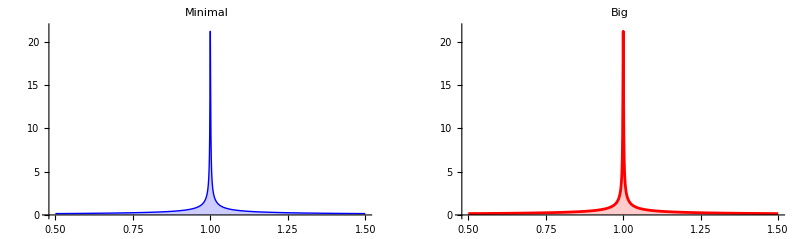

```mathematica
GraphicsRow[{DoSplot[1+x**x**x-z,{0.5,1.5},PlotLabel->"Minimal"],DoSplot[1+x**x**x-z,{0.5,1.5},LinearizationType->"Big",PlotLabel->"Big",PlotStyle->{Red}]}]
```

## Limiting eigenvalue distribution for randomly generated noncommutative polynomials of degree 3 in two Wigner matrices

Example of a generated polynomial

```mathematica
1-z+GeneratePolynomial[{x,y},{2,4,8},"Real"]
```

1-1.52537 x+1.97101 y-z+8.38746 x**x-0.151023 x**y-0.151023 y**x-3.65231 y**y-9.36504 x**x**x-3.31932 x**x**y+0.00796495 x**y**x+0.388089 x**y**y-3.31932 y**x**x-3.59479 y**x**y+0.388089 y**y**x+1.92581 y**y**y

We generate noncommutative self-adjoint polynomials. For each polynomial we compute its minimal linearization, solve the Dyson equation for the linearization on the interval [-130, 130], and recover the self-consistent density of states for the polynomial. We then plot the corresponding density. Notice that some polynomials have bimodal structure (we don’t see this very often)

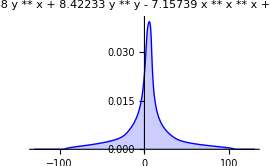
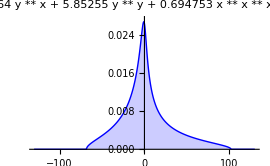
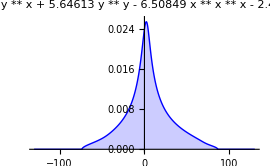
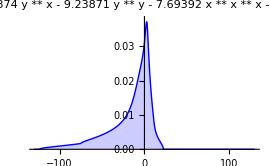
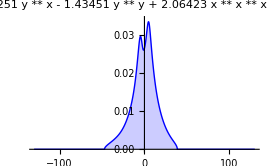
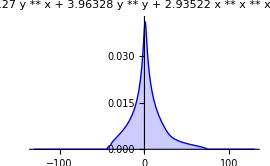
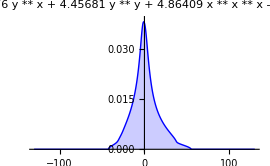
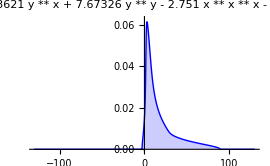

```mathematica
p={};
Do[Poly=1-z+GeneratePolynomial[{x,y},{2,4,8},"Real"];

PolyLabel=StringJoin[Characters[ToString[Poly]][[1;;Ceiling[Length[Characters[ToString[Poly]]]/4]]]]<>"\n "<>StringJoin[Characters[ToString[Poly]][[Ceiling[Length[Characters[ToString[Poly]]]/4]+1;;Ceiling[2*Length[Characters[ToString[Poly]]]/4]]]]<>"\n "<>StringJoin[Characters[ToString[Poly]][[Ceiling[2*Length[Characters[ToString[Poly]]]/4]+1;;Ceiling[3*Length[Characters[ToString[Poly]]]/4]]]]<>"\n "<>StringJoin[Characters[ToString[Poly]][[Ceiling[3*Length[Characters[ToString[Poly]]]/4]+1;;Ceiling[Length[Characters[ToString[Poly]]]]]]];

p=Append[p,DoSplot[Poly,{-130,130},GridNumber->1000,PlotLabel->Style[PolyLabel,FontColor->Red,FontSize->8]]]
,{ind,10}];
Table[Table[p[[ind*2+j]],{j,2}],{ind,0,4}]
```

### Diagonal entries of Im M

The conjecture is that all diagonal entries of Im M vanish if and only if the (1,1) entry of Im M vanishes. In other words, Im M either has full rank or is equal to zero. In order to check this numerically for a concrete polynomial, we can plot the self-consistent density of states, and then plot the diagonal entries of Im M in the vicinity of the edge of the support (see example below)

```mathematica
Poly=1+GeneratePolynomial[{x,y},{2,4,8},"Real"];
```

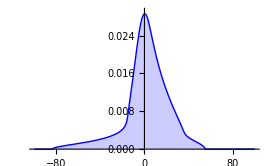

```mathematica
DoSplot[1+Poly-z,{-100,100}]
```

```mathematica
Linearization=MinimalLinearization[Poly-z,"MachinePrecision"];
KK=500000; ϵϵ=0.000001;
DData=Table[Table[{50+j*5/100,Sort[Table[Im[IterativelySolveMDE2[Linearization,z, 50+j*5/100+0.000001*ⅈ,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ][[ind,ind]]],{ind,5}]][[k]]},{j,100}],{k,5}];
```

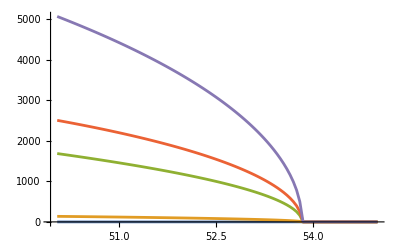

```mathematica
ListLinePlot[DData, PlotRange->All]
```

It looks like one of the diagonal entries is zero...

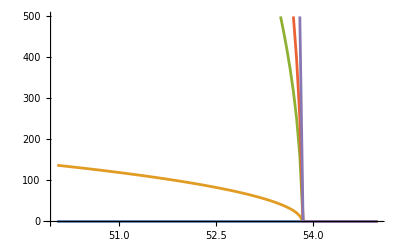

```mathematica
ListLinePlot[DData, PlotRange->{-1,500}]
```

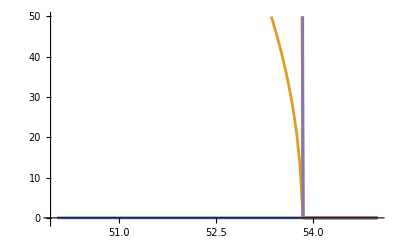

```mathematica
ListLinePlot[DData, PlotRange->{-1,50}]
```

... but in fact this is just the (1,1) entry which is much smaller than all other entries.

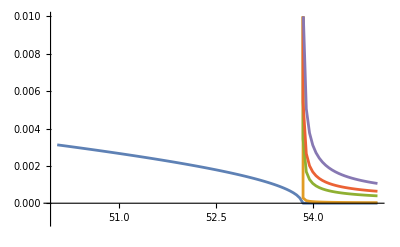

```mathematica
ListLinePlot[DData, PlotRange->{-0.001,0.01}]
```

### Family of polynomials with bimodal densities

Here we plot the density of states for a family of polynomials 1+x^4+αx^2. We see that for α>0 and α<0 the density looks differently. More importantly, for α<0 the density blows up at two different point, which we haven’t seen before.

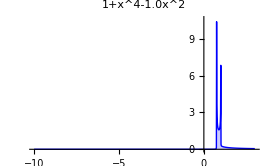
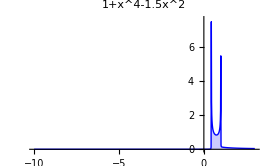
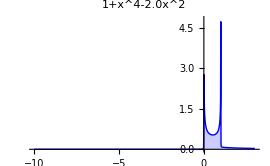
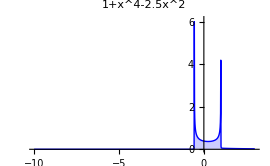
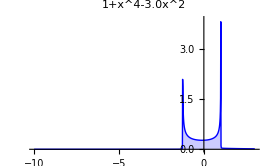
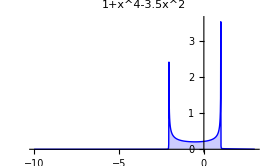
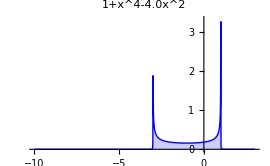
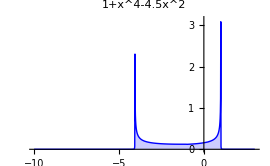

```mathematica
p=Table[DoSplot[1+x**x**x**x-(1+j/2)*x**x-z,{-10,3},PlotLabel->"1+x^4-"<>ToString[N[1+j/2,2]]<>"x^2"],{j,0,9}];
Table[Table[p[[2*ind+j]],{j,2}],{ind,0,4}]
```

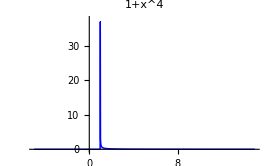
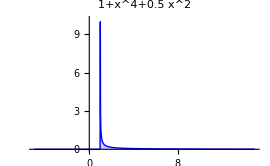
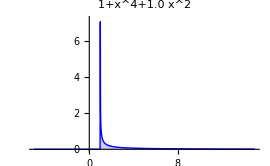
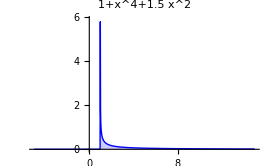
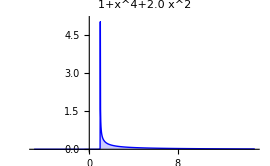
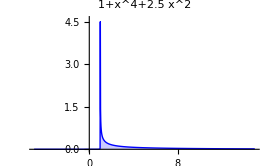
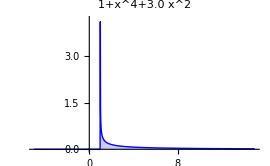
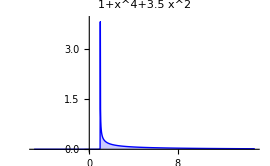

```mathematica
q=Join[{DoSplot[1+x**x**x**x-z,{-5,15},PlotLabel->"1+x^4"],DoSplot[1+x**x**x**x+0.5*x**x-z,{-5,15},PlotLabel->"1+x^4+0.5 x^2"]},Table[DoSplot[1+x**x**x**x+(j/2)*x**x-z,{-5,15},PlotLabel->"1+x^4+"<>ToString[N[j/2,2]]<>" x^2"],{j,2,9}]];
Table[Table[q[[2*ind+j]],{j,2}],{ind,0,4}]
```

### Compare the smallest eigenvalues of Im M for the big and the minimal linearization

The conjecture is that for the minimal linearization all eigenvalues of Im M vanish together (Im M is either full rank or a zero matrix), while for the big linearization Im M may not be full rank.

Conclusion :  λ (Im M) can be equivalent to Tr (Im M) only for minimal linearization

Example 1:

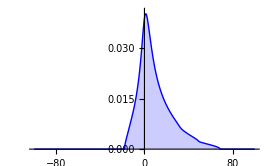

```mathematica
Poly=1+GeneratePolynomial[{x,y},{2,4,8},"Real"];
DoSplot[1+Poly-z,{-100,100}]
```

We start by plotting two smallest eigenvalues of Im M near the edge for the Minimal linearization

```mathematica
MatrixIm[M_]:=(M - ConjugateTranspose[M])/(2 * ⅈ);
```

```mathematica
Linearization=MinimalLinearization[Poly-z,"MachinePrecision"];
KK=500000; ϵϵ=0.00001;
DData=Table[Table[{N[64+j*5/100],Eigenvalues[MatrixIm[IterativelySolveMDE2[Linearization,z, 64+j*5/100+0.000001*ⅈ,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ]]][[-ind]]},{j,100}],{ind,2}];
```

1000010.0332368

1000010.0332368

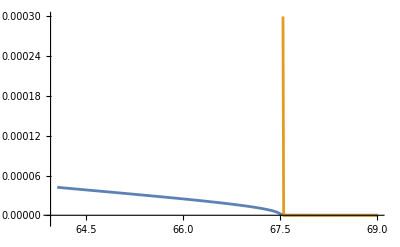

```mathematica
ListLinePlot[DData,PlotRange->{-0.00001,0.0003}]
```

Here we plot three smallest eigenvalues of Im M near the edge for the Big linearization

```mathematica
Linearization=BigLinearization[Poly-z];
KK=500000; ϵϵ=0.00001;
DData=Table[Table[{N[64+j*5/100],Eigenvalues[MatrixIm[IterativelySolveMDE2[Linearization,z, 64+j*5/100+0.000001*ⅈ,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ]]][[-ind]]},{j,100}],{ind,3}];
```

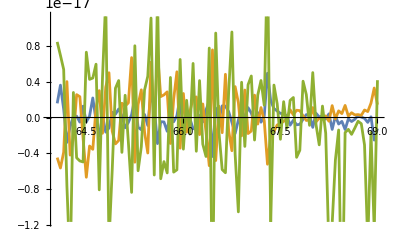

```mathematica
ListLinePlot[DData]
```

Example 2:

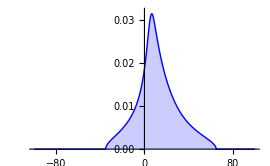

```mathematica
Poly=1+GeneratePolynomial[{x,y},{2,4,8},"Real"];
DoSplot[1+Poly-z,{-100,100}]
```

Again, we plot two smallest eigenvalues of Im M near the edge for the Minimal linearization

```mathematica
Linearization=MinimalLinearization[Poly-z,"MachinePrecision"];
KK=500000; ϵϵ=0.00001;
DData=Table[Table[{N[62+j*5/100],Eigenvalues[MatrixIm[IterativelySolveMDE2[Linearization,z, 62+j*5/100+0.000001*ⅈ,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ]]][[-ind]]},{j,100}],{ind,2}];
```

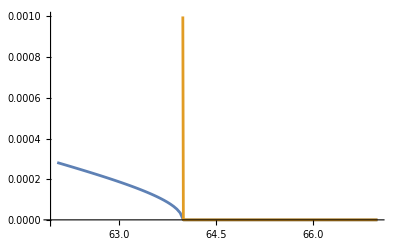

```mathematica
ListLinePlot[DData,PlotRange->{-0.00001,0.001}]
```

We plot three smallest eigenvalues of Im M near the edge for the Big linearization

```mathematica
Linearization=BigLinearization[Poly-z];
KK=500000; ϵϵ=0.00001;
DData=Table[Table[{N[62+j*5/100],Eigenvalues[MatrixIm[IterativelySolveMDE2[Linearization,z, 62+j*5/100+0.000001*ⅈ,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ]]][[-ind]]},{j,100}],{ind,3}];
```

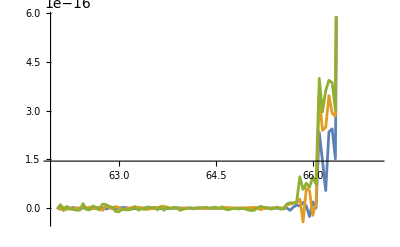

```mathematica
ListLinePlot[DData]
```